```mathematica
(*Results for Region 1 with different methods*)
(*Fixed Interval Method*)
RectangleFixed=1/2 t √ρ (2 (2-ⅇ^(-(t^2 ρ)/2)) t √ρ-4 √2 (-1+t^2 ρ) DawsonF[(t √ρ)/(√2)]+√(2 π) Erf[(t √ρ)/(√2)])
FullSimplify[%/. t->1]
RFixedTable =Table[%,{ρ,1,100}];
```

1/2 t √ρ (2 (2-ⅇ^(-(t^2 ρ)/2)) t √ρ-4 √2 (-1+t^2 ρ) DawsonF[(t √ρ)/(√2)]+√(2 π) Erf[(t √ρ)/(√2)])

(2-ⅇ^(-ρ/2)) ρ+(√ρ (-4 (-1+ρ) DawsonF[(√ρ)/(√2)]+√π Erf[(√ρ)/(√2)]))/(√2)

```mathematica
(*Cartesian Method*)
RectangleCartesian = -ⅇ^(-(t^2 ρ)/2) t^2 ρ+(t √ρ (-24 DawsonF[(t √ρ)/(√2)]+√π Erf[(t √ρ)/(√2)]))/(√2)-t^2 ρ (-20+HypergeometricPFQ[{1,1},{-1/2,2},-(t^2 ρ)/2]-3 HypergeometricPFQ[{1,1},{1/2,2},-(t^2 ρ)/2]+6 HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2])+1/3 t^4 ρ^2 (-18 HypergeometricPFQ[{1/2,1},{3/2,3/2},-(t^2 ρ)/2]+24 HypergeometricPFQ[{1/2,1},{3/2,5/2},-(t^2 ρ)/2]-24 HypergeometricPFQ[{1/2,2},{3/2,5/2},-(t^2 ρ)/2]+6 HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2]-8 HypergeometricPFQ[{1,1},{2,5/2},-(t^2 ρ)/2]+3 HypergeometricPFQ[{1,1},{5/2,3},-(t^2 ρ)/2])
FullSimplify[%/. t->1]
RCartesianTable =Table[%,{ρ,1,100}];
```

-ⅇ^(-(t^2 ρ)/2) t^2 ρ+(t √ρ (-24 DawsonF[(t √ρ)/(√2)]+√π Erf[(t √ρ)/(√2)]))/(√2)-t^2 ρ (-20+HypergeometricPFQ[{1,1},{-1/2,2},-(t^2 ρ)/2]-3 HypergeometricPFQ[{1,1},{1/2,2},-(t^2 ρ)/2]+6 HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2])+1/3 t^4 ρ^2 (-18 HypergeometricPFQ[{1/2,1},{3/2,3/2},-(t^2 ρ)/2]+24 HypergeometricPFQ[{1/2,1},{3/2,5/2},-(t^2 ρ)/2]-24 HypergeometricPFQ[{1/2,2},{3/2,5/2},-(t^2 ρ)/2]+6 HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2]-8 HypergeometricPFQ[{1,1},{2,5/2},-(t^2 ρ)/2]+3 HypergeometricPFQ[{1,1},{5/2,3},-(t^2 ρ)/2])

-ⅇ^(-ρ/2) ρ+(√ρ (-24 DawsonF[(√ρ)/(√2)]+√π Erf[(√ρ)/(√2)]))/(√2)-ρ (-20+HypergeometricPFQ[{1,1},{-1/2,2},-ρ/2]-3 HypergeometricPFQ[{1,1},{1/2,2},-ρ/2]+6 HypergeometricPFQ[{1,1},{3/2,2},-ρ/2])+1/3 ρ^2 (-18 HypergeometricPFQ[{1/2,1},{3/2,3/2},-ρ/2]+24 HypergeometricPFQ[{1/2,1},{3/2,5/2},-ρ/2]-24 HypergeometricPFQ[{1/2,2},{3/2,5/2},-ρ/2]+6 HypergeometricPFQ[{1,1},{3/2,2},-ρ/2]-8 HypergeometricPFQ[{1,1},{2,5/2},-ρ/2]+3 HypergeometricPFQ[{1,1},{5/2,3},-ρ/2])

```mathematica
(*Expected relation*)
S= √(π/2)*√ρ*t
FullSimplify[%/. t->1]
RExpectedTable =Table[%,{ρ,1,100}];
```

√(π/2) t √ρ

√(π/2) √ρ

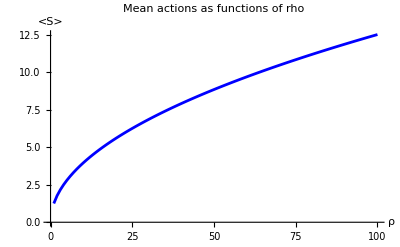

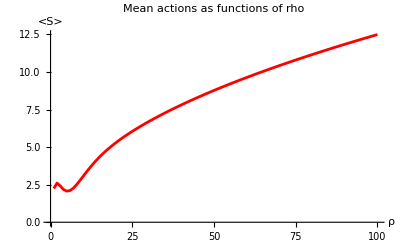

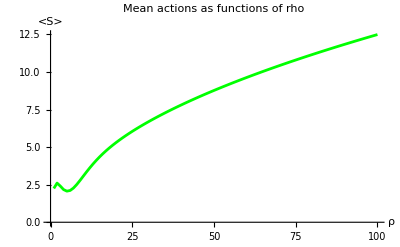

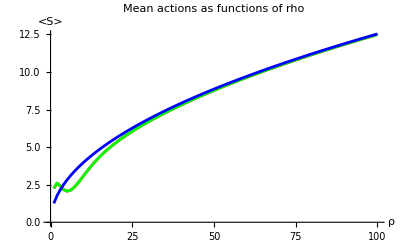

```mathematica
(*Graphs*)
RFixedGraph=ListLinePlot[RFixedTable,PlotStyle->Red];
RCartesianGraph=ListLinePlot[RCartesianTable,PlotStyle->Green];
RExpectedGraph=ListLinePlot[RExpectedTable,PlotStyle->Blue];
Show[RExpectedGraph,PlotLabel->"Mean actions as functions of rho",AxesLabel->{"ρ","<S>"}]
Show[RFixedGraph,PlotLabel->"Mean actions as functions of rho",AxesLabel->{"ρ","<S>"}]
Show[RCartesianGraph,PlotLabel->"Mean actions as functions of rho",AxesLabel->{"ρ","<S>"}]
Show[RFixedGraph,RCartesianGraph,RExpectedGraph,PlotLabel->"Mean actions as functions of rho",AxesLabel->{"ρ","<S>"}]
```